Data Import

```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210519_time_windows_and_OR_model"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package-2.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
datafull=Import["../data/csp_manipulated_205496.csv"];
```

Investigation of Constraints Impact in Time Windows

Fixed Step Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataFixedstep1=snetworkdatabinned[9,11,datafull];]
```

{51.3849,Null}

```mathematica
graphsandnodenumbers1=snetworkgraph[widthdataFixedstep1[[1]],widthdataFixedstep1[[2]],2,7,400,Green];
modularityvalues1=N@GraphAssortativity[graphsandnodenumbers1[[1]],FindGraphCommunities[graphsandnodenumbers1[[1]]],"Normalized"->False];
```

```mathematica
singlerandomgraphsdegfxd1=randomizinggraphdegfxd[graphsandnodenumbers1[[1]]];
singlerandomerdrenmodularityvalues1=N@GraphAssortativity[singlerandomgraphsdegfxd1,FindGraphCommunities[singlerandomgraphsdegfxd1],"Normalized"->False];
singlerandomgraphscomm1=randomizinggraphmod[graphsandnodenumbers1[[1]]];
singlerandomcommmodularityvalues1=N@GraphAssortativity[singlerandomgraphscomm1,FindGraphCommunities[singlerandomgraphscomm1],"Normalized"->False];
```

```mathematica
AbsoluteTiming[Zscoresmodularity1=zscorefunctionfortwonullmodels[graphsandnodenumbers1[[1]]];]
```

{67.2994,Null}

```mathematica
bucketnode11=graphsandnodenumbers1[[2]]
```

95

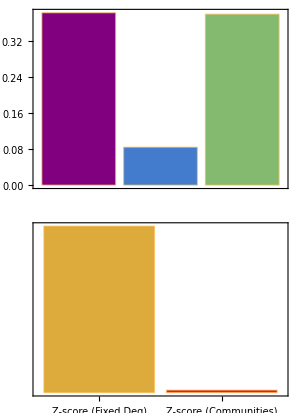

```mathematica
modval=modularityvalues1;
rndmoddegrees=singlerandomerdrenmodularityvalues1;
rndmodcomm=singlerandomcommmodularityvalues1;
zscoredegrees=Zscoresmodularity1[[1]];
zscorecomm=Zscoresmodularity1[[2]];
labels={"Modularity","Sng. Rnd. Mod.\n(Fixed Deg)","Sng. Rnd. Mod.\n(Communities)","Z-score\n(Fixed Deg)","Z-score\n(Communities)"};
Legended[Framed[GraphicsColumn[{BarChart[{modval,rndmoddegrees,rndmodcomm},ChartStyle->{Purple,RGBColor[{0.266122,0.486664,0.802529}],RGBColor[{0.513417,0.72992,0.440682}]},ChartLabels->labels[[{1,2,3}]](*,ScalingFunctions->"Log"*),Frame->True,FrameTicks->{{All,None},{None,{{1,labels[[1]]},{2,labels[[2]]},{3,labels[[3]]}}}},PlotRange->{{0.5,3.5},All}],BarChart[{zscoredegrees,zscorecomm},ChartStyle->{RGBColor[{0.863512,0.670771,0.236564}],RGBColor[{0.857359,0.131106,0.132128}]}(*,ScalingFunctions->"Log"*),Frame->True,PlotRange->{{0.5,2.5},All},FrameTicks->{{None,All},{{{1,labels[[4]]},{2,labels[[5]]}},None}}]},ImageSize->300,Spacings->5,PlotLabel->"Complete Data"],FrameMargins->5,FrameStyle->DotDashed],Placed[Rotate["Complete Data",90Degree],{0.01,0.5}]]
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataFixedstep1=snetworkdatabinned[10,0.05,datafull];]
```

{165.175,Null}

```mathematica
graphsandnodenumbers2=snetworkgraph[thicknessdataFixedstep1[[1]],thicknessdataFixedstep1[[2]],2,7,400,RGBColor[0.1,0.5,1.]];
modularityvalues2=N@GraphAssortativity[graphsandnodenumbers2[[1]],FindGraphCommunities[graphsandnodenumbers2[[1]]],"Normalized"->False];
```

```mathematica
singlerandomgraphsdegfxd2=randomizinggraphdegfxd[graphsandnodenumbers2[[1]]];
singlerandomerdrenmodularityvalues2=N@GraphAssortativity[singlerandomgraphsdegfxd2,FindGraphCommunities[singlerandomgraphsdegfxd2],"Normalized"->False];
singlerandomgraphscomm2=randomizinggraphmod[graphsandnodenumbers2[[1]]];
singlerandomcommmodularityvalues2=N@GraphAssortativity[singlerandomgraphscomm2,FindGraphCommunities[singlerandomgraphscomm2],"Normalized"->False];
```

```mathematica
AbsoluteTiming[Zscoresmodularity2=zscorefunctionfortwonullmodels[graphsandnodenumbers2[[1]]];]
```

{14.2857,Null}

```mathematica
bucketnode21=graphsandnodenumbers2[[2]]
```

33

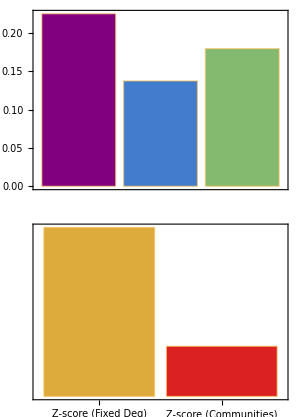

```mathematica
modval=modularityvalues2;
rndmoddegrees=singlerandomerdrenmodularityvalues2;
rndmodcomm=singlerandomcommmodularityvalues2;
zscoredegrees=Zscoresmodularity2[[1]];
zscorecomm=Zscoresmodularity2[[2]];
labels={"Modularity","Sng. Rnd. Mod.\n(Fixed Deg)","Sng. Rnd. Mod.\n(Communities)","Z-score\n(Fixed Deg)","Z-score\n(Communities)"};
Legended[Framed[GraphicsColumn[{BarChart[{modval,rndmoddegrees,rndmodcomm},ChartStyle->{Purple,RGBColor[{0.266122,0.486664,0.802529}],RGBColor[{0.513417,0.72992,0.440682}]},ChartLabels->labels[[{1,2,3}]](*,ScalingFunctions->"Log"*),Frame->True,FrameTicks->{{All,None},{None,{{1,labels[[1]]},{2,labels[[2]]},{3,labels[[3]]}}}},PlotRange->{{0.5,3.5},All}],BarChart[{zscoredegrees,zscorecomm},ChartStyle->{RGBColor[{0.863512,0.670771,0.236564}],RGBColor[{0.857359,0.131106,0.132128}]}(*,ScalingFunctions->"Log"*),Frame->True,PlotRange->{{0.5,2.5},All},FrameTicks->{{None,All},{{{1,labels[[4]]},{2,labels[[5]]}},None}}]},ImageSize->300,Spacings->5,PlotLabel->"Complete Data"],FrameMargins->5,FrameStyle->DotDashed],Placed[Rotate["Complete Data",90Degree],{0.01,0.5}]]
```

Fixed Bucket Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataFixedbucket1=snetworkdatafxdbucket[9,bucketnode11,datafull];]
```

{9.63334,Null}

```mathematica
graphsandnodenumbers3=snetworkgraph[widthdataFixedbucket1[[1]],widthdataFixedbucket1[[2]],2,7,400,Green];
modularityvalues3=N@GraphAssortativity[graphsandnodenumbers3[[1]],FindGraphCommunities[graphsandnodenumbers3[[1]]],"Normalized"->False];
```

```mathematica
singlerandomgraphsdegfxd3=randomizinggraphdegfxd[graphsandnodenumbers3[[1]]];
singlerandomerdrenmodularityvalues3=N@GraphAssortativity[singlerandomgraphsdegfxd3,FindGraphCommunities[singlerandomgraphsdegfxd3],"Normalized"->False];
singlerandomgraphscomm3=randomizinggraphmod[graphsandnodenumbers3[[1]]];
singlerandomcommmodularityvalues3=N@GraphAssortativity[singlerandomgraphscomm3,FindGraphCommunities[singlerandomgraphscomm3],"Normalized"->False];
```

```mathematica
AbsoluteTiming[Zscoresmodularity3=zscorefunctionfortwonullmodels[graphsandnodenumbers3[[1]]];]
```

{55.3194,Null}

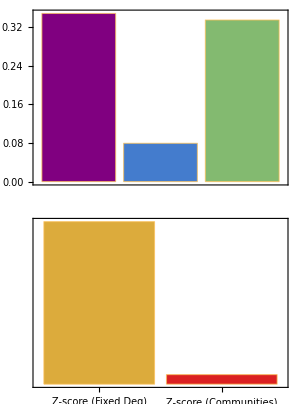

```mathematica
modval=modularityvalues3;
rndmoddegrees=singlerandomerdrenmodularityvalues3;
rndmodcomm=singlerandomcommmodularityvalues3;
zscoredegrees=Zscoresmodularity3[[1]];
zscorecomm=Zscoresmodularity3[[2]];
labels={"Modularity","Sng. Rnd. Mod.\n(Fixed Deg)","Sng. Rnd. Mod.\n(Communities)","Z-score\n(Fixed Deg)","Z-score\n(Communities)"};
Legended[Framed[GraphicsColumn[{BarChart[{modval,rndmoddegrees,rndmodcomm},ChartStyle->{Purple,RGBColor[{0.266122,0.486664,0.802529}],RGBColor[{0.513417,0.72992,0.440682}]},ChartLabels->labels[[{1,2,3}]](*,ScalingFunctions->"Log"*),Frame->True,FrameTicks->{{All,None},{None,{{1,labels[[1]]},{2,labels[[2]]},{3,labels[[3]]}}}},PlotRange->{{0.5,3.5},All}],BarChart[{zscoredegrees,zscorecomm},ChartStyle->{RGBColor[{0.863512,0.670771,0.236564}],RGBColor[{0.857359,0.131106,0.132128}]}(*,ScalingFunctions->"Log"*),Frame->True,PlotRange->{{0.5,2.5},All},FrameTicks->{{None,All},{{{1,labels[[4]]},{2,labels[[5]]}},None}}]},ImageSize->300,Spacings->5,PlotLabel->"Complete Data"],FrameMargins->5,FrameStyle->DotDashed],Placed[Rotate["Complete Data",90Degree],{0.01,0.5}]]
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataFixedbucket1=snetworkdatafxdbucket[10,bucketnode21,datafull];]
```

{12.2503,Null}

```mathematica
graphsandnodenumbers4=snetworkgraph[thicknessdataFixedbucket1[[1]],thicknessdataFixedbucket1[[2]],2,7,400,Green];
modularityvalues4=N@GraphAssortativity[graphsandnodenumbers4[[1]],FindGraphCommunities[graphsandnodenumbers4[[1]]],"Normalized"->False];
```

```mathematica
singlerandomgraphsdegfxd4=randomizinggraphdegfxd[graphsandnodenumbers4[[1]]];
singlerandomerdrenmodularityvalues4=N@GraphAssortativity[singlerandomgraphsdegfxd4,FindGraphCommunities[singlerandomgraphsdegfxd4],"Normalized"->False];
singlerandomgraphscomm4=randomizinggraphmod[graphsandnodenumbers4[[1]]];
singlerandomcommmodularityvalues4=N@GraphAssortativity[singlerandomgraphscomm4,FindGraphCommunities[singlerandomgraphscomm4],"Normalized"->False];
```

```mathematica
AbsoluteTiming[Zscoresmodularity4=zscorefunctionfortwonullmodels[graphsandnodenumbers4[[1]]];]
```

{22.4323,Null}

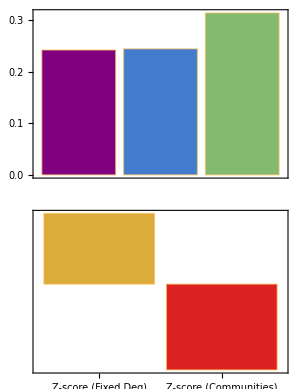

```mathematica
modval=modularityvalues4;
rndmoddegrees=singlerandomerdrenmodularityvalues4;
rndmodcomm=singlerandomcommmodularityvalues4;
zscoredegrees=Zscoresmodularity4[[1]];
zscorecomm=Zscoresmodularity4[[2]];
labels={"Modularity","Sng. Rnd. Mod.\n(Fixed Deg)","Sng. Rnd. Mod.\n(Communities)","Z-score\n(Fixed Deg)","Z-score\n(Communities)"};
Legended[Framed[GraphicsColumn[{BarChart[{modval,rndmoddegrees,rndmodcomm},ChartStyle->{Purple,RGBColor[{0.266122,0.486664,0.802529}],RGBColor[{0.513417,0.72992,0.440682}]},ChartLabels->labels[[{1,2,3}]](*,ScalingFunctions->"Log"*),Frame->True,FrameTicks->{{All,None},{None,{{1,labels[[1]]},{2,labels[[2]]},{3,labels[[3]]}}}},PlotRange->{{0.5,3.5},All}],BarChart[{zscoredegrees,zscorecomm},ChartStyle->{RGBColor[{0.863512,0.670771,0.236564}],RGBColor[{0.857359,0.131106,0.132128}]}(*,ScalingFunctions->"Log"*),Frame->True,PlotRange->{{0.5,2.5},All},FrameTicks->{{None,All},{{{1,labels[[4]]},{2,labels[[5]]}},None}}]},ImageSize->300,Spacings->5,PlotLabel->"Complete Data"],FrameMargins->5,FrameStyle->DotDashed],Placed[Rotate["Complete Data",90Degree],{0.01,0.5}]]
```